```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/code"];
```

## Problem 1

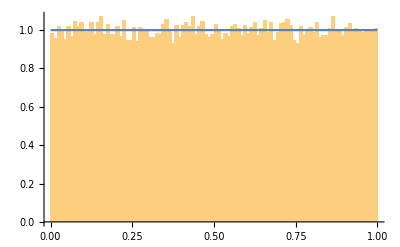

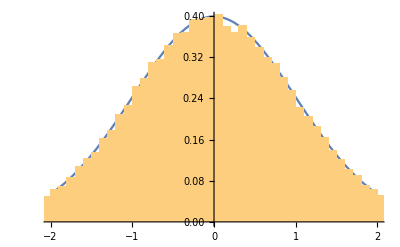

```mathematica
data = ReadList["!./p1 100000", {Number, Number}];
drand48 = Histogram[data[[All,1]], 100, PDF];
gausrand48 = Histogram[data[[All,2]], 100, PDF];
gaus = Plot[PDF[NormalDistribution[0,1],x],{x,-2,2}];
rand = Plot[1, {x, 0, 1}];
Show[drand48, rand]
Show[gaus, gausrand48]
```

## Problem 2

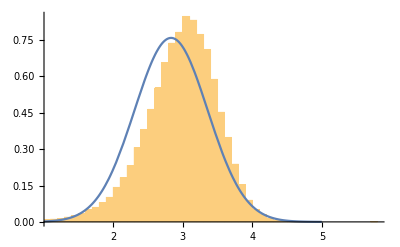

```mathematica
SetDirectory["/home/ethan/spring20/comphys/week7/class"];
data = ReadList["!./a.out 1 2 4 1 100000"];
naive= Plot[PDF[NormalDistribution[Log[17],0.526],x],{x,0, 5}];
soph = Histogram[data,100, "PDF"];
Show[soph, naive]
```